# Lab 8: Semiconductor Detectors

J.R. Powers-Luhn
jpowersl@vols.utk.edu
Station 1
Partner: Tanner Jacobi

## Using the MCA

1. For each conversion gain, calculate the voltage width per channel.

```mathematica
conversionGains=Table[2^n,{n,8,14}]
```

{256,512,1024,2048,4096,8192,16384}

According to the spec sheet for the Ortex ASPEC-927 MCA (http://www.ortec-online.com/products/electronics/multichannel-analyzers-mca/basic-analog/aspec-927), the voltage range for our MCA is 0-10V.

```mathematica
voltageWidthPerChannel=10/conversionGains//N
```

{0.0390625,0.0195313,0.00976563,0.00488281,0.00244141,0.0012207,0.000610352}

The voltage per channel for the various settings of the Conversion Gain parameter are in the table below:

```mathematica
TableForm[Multicolumn[Join[conversionGains, voltageWidthPerChannel],2]//First, TableHeadings->{None,{"Conversion Gain","Voltage width per Channel"}}]
```

Conversion Gain | Voltage width per Channel
256 | 0.0390625
512 | 0.0195313
1024 | 0.00976563
2048 | 0.00488281
4096 | 0.00244141
8192 | 0.0012207
16384 | 0.000610352

2. Using the conversions from 1, determine the voltage measured by the MCA for the determined channel peak number for each of the four conversion gains.

```mathematica
peaks={324, 2430, 648, 1298};
conversionGains={512, 4096, 1024, 2048};
voltPeaks=peaks*10/conversionGains//N
```

{6.32813,5.93262,6.32813,6.33789}

```mathematica
Mean[voltPeaks]
Mean[{voltPeaks[[1]],voltPeaks[[3]],voltPeaks[[4]]}]
StandardDeviation[voltPeaks]
(Mean[voltPeaks]-voltPeaks[[2]])/StandardDeviation[voltPeaks]
```

6.23169

6.33138

0.199435

1.4996

The peak channel on the MCA software corresponded to a voltage of 6.23V, or 6.33V if the outlier (conversion gain of 4096, approximately 1.5σ below the mean value) is excluded. Error analysis was not conducted as no uncertainty in the 10V max was provided by the MCA manufacturer and the error in the number of bits in the address space was assumed to be zero.

It is assumed that, as the 4096 channel data were collected first while the other settings were collected in rapid

3. From the data recorded, make a properly formatted table of the data (conversion gain, peak channel number, and voltage corresponding to the channel peak number).

```mathematica
TableForm[Multicolumn[Join[conversionGains,peaks,voltPeaks],3]//First,TableHeadings->{None,{"Conversion Gain", "Peak Channel", "Peak Voltage"}}]
```

Conversion Gain | Peak Channel | Peak Voltage
512 | 324 | 6.32813
4096 | 2430 | 5.93262
1024 | 648 | 6.32813
2048 | 1298 | 6.33789

4. From the data in the table and in a text-style cell, discuss the trends seen in the peak channel number and corresponding voltage to the peak channel number. Which one is constant and which one changes? Why does that one change? Does it make sense?

As expected, the peak channel changes while the peak voltage remains constant. Altering the number of channels (bits in the address space) only changes the “binning” when processing the incoming signals. Therefore the size of the voltage range represented by each channel changes, but the input voltage range remains from 0-10V.

MCA Linearity

1. From the spectrum saved (should contain a total of 15 peaks), find the peak channel number (i.e., the average channel number used in a Gaussian fit) for each of the 15 peak regions.
	a. Note: This can be found by multiplying the number of counts by the channel number, summing up this quantity over the Gaussian region, and then dividing by the total number of counts observed in this region (area of Gaussian).
	b. Note: This can also be accomplished by fitting a Gaussian to each of the 15 peaks, where the initial guess in the fit can be changed to near the peak of each of the 15 peaks.

```mathematica
datafolder=NotebookDirectory[]<>"data/maestro/Spectra/";
datafile="thulab8mcalinear.Spe";
data=ToExpression[StringSplit[Import[datafolder<>datafile],"\n"][[13;;-15]]];
peaks=FindPeaks[data,50]
deltaV=10.0/ToExpression[StringSplit[StringSplit[Import[datafolder<>datafile],"\n"][[12]]][[2]]];
```

{{112,15451},{336,12936},{604,12252},{885,12664},{1168,16397},{1453,10244},{1716,16110},{2012,12512},{2293,15461},{2596,8738},{2831,15361},{3126,13764},{3386,9935},{3680,10523},{3885,9980}}

2. For the data in step 1, convert the channel number to voltage.

```mathematica
voltPeaks=peaks[[;;,1]]*deltaV
```

{0.273504,0.820513,1.47497,2.16117,2.85226,3.54823,4.19048,4.91331,5.59951,6.33944,6.91331,7.6337,8.26862,8.98657,9.48718}

```mathematica
TableForm[voltPeaks]
```

0.273504
0.820513
1.47497
2.16117
2.85226
3.54823
4.19048
4.91331
5.59951
6.33944
6.91331
7.6337
8.26862
8.98657
9.48718

The voltages corresponding to the 15 peaks are printed in table form above.

3. From the data in step 2, create a properly formatted plot of MCA measured voltage vs. input voltage (y on x). This is the integral nonlinearity plot of the MCA, similar to figure 2 in the introduction.

```mathematica
measuredpeaks=Sort[{6.56,0.28, 0.84, 1.50, 2.20,2.92,3.64,4.32,5.04,5.76,7.12,7.84,8.60,9.20,9.80}]
```

{0.28,0.84,1.5,2.2,2.92,3.64,4.32,5.04,5.76,6.56,7.12,7.84,8.6,9.2,9.8}

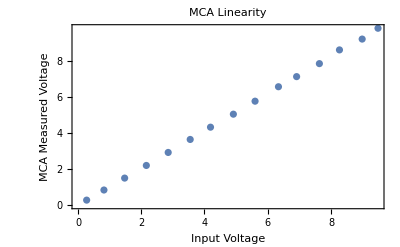

```mathematica
mcaplot=ListPlot[Multicolumn[Join[voltPeaks,measuredpeaks],2]//First,
ImageSize->Full,Frame->True,FrameLabel->{Style["Input Voltage",18],Style["MCA Measured Voltage",18]},FrameTicksStyle->Directive[Black,16],PlotLabel->Style["MCA Linearity",24]]
```

4. Using equation 1, determine the integral nonlinearity for each of the 15 data points. Place data in a properly formatted table (input voltage, output voltage determined via the Gaussian fit, and integral nonlinearity.

```mathematica
formatnum[list_,fig_,dec_]:=Table[NumberForm[list[[i]],{fig,dec}],{i,Length[list]}]
```

```mathematica
equationOne[Vnom_,Vact_,Vmax_]:=(Vnom-Vact)*100/Vmax;
TableForm[Multicolumn[Join[formatnum[measuredpeaks,4,2],formatnum[voltPeaks,4,2],formatnum[equationOne[measuredpeaks,voltPeaks,10],4,2]],3]//First,TableHeadings->{None, {"Input Voltage (±0.01V)", "Measured Peak Voltage (V)", "Integral Nonlinearity (%)"}}]
```

Input Voltage (±0.01V) | Measured Peak Voltage (V) | Integral Nonlinearity (%)
0.28 | 0.27 | 0.06
0.84 | 0.82 | 0.19
1.50 | 1.47 | 0.25
2.20 | 2.16 | 0.39
2.92 | 2.85 | 0.68
3.64 | 3.55 | 0.92
4.32 | 4.19 | 1.30
5.04 | 4.91 | 1.27
5.76 | 5.60 | 1.60
6.56 | 6.34 | 2.21
7.12 | 6.91 | 2.07
7.84 | 7.63 | 2.06
8.60 | 8.27 | 3.31
9.20 | 8.99 | 2.13
9.80 | 9.49 | 3.13

5. Looking at the plot from 3 and data in 4, comment on the integral nonlinearity of the MCA over the input voltage range. Is the integral nonlinearity zero, constant, and/or varying across the voltage range?

```mathematica
line=LinearModelFit[Multicolumn[Join[measuredpeaks,equationOne[measuredpeaks,voltPeaks,10]],2]//First,x,x]
```

FittedModel[-0.174739+0.319935 x]

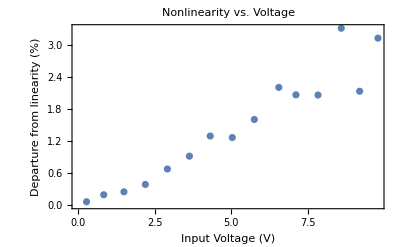

```mathematica
pp=ListPlot[Multicolumn[Join[measuredpeaks,equationOne[measuredpeaks,voltPeaks,10]],2]//First,ImageSize->Full,PlotLabel->Style["Nonlinearity vs. Voltage",24],Frame->True,FrameLabel->{Style["Input Voltage (V)",18],Style["Departure from linearity (%)",18]},FrameTicksStyle->Directive[16]]
```

The integral nonlinearity increases with input voltage. In this range it is not possible to determine whether or not the relationship is approximately linear or if it follows some other curve. Certainly the deviation from a linear value also increased with time, though the inconsistent curve suggests that noise was introduced at a higher magnitude as a function of voltage.

MCA Dead Time

1. From the data collected, make a properly formatted table of the time delay between amplifier output peaks and amplifier output amplitude for the first (larger) amplifier analog signal.

```mathematica
data={{5.44,3.72},{1.08,3.58},{3.00,3.63},{7.04,3.73},{9.00,3.72}};
TableForm[Multicolumn[Join[formatnum[data[[;;,1]],3,2],formatnum[data[[;;,2]],3,2]],2]//First,TableHeadings->{None,{"Voltage (±0.01V)","Delay (±0.01μs)"}}]
```

Voltage (±0.01V) | Delay (±0.01μs)
5.44 | 3.72
1.08 | 3.58
3.00 | 3.63
7.04 | 3.73
9.00 | 3.72

2. From the table of data in step 1, identify if the dead time is a function of input amplitude or not.

```mathematica
Correlation[data[[;;,1]],data[[;;,2]]]
```

0.912855

```mathematica
ft=LinearModelFit[data,x,x]
```

FittedModel[3.57625+0.0195124 x]

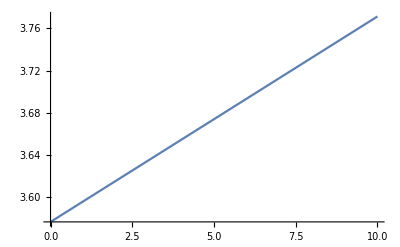

3.57625

3.77138

```mathematica
Plot[ft[x],{x,0,10}]
ft[0]
ft[10]
```

From the data it appears that dead time is a function of input amplitude, with the two values 91% correlated. Assuming a linear fit, the deadtime for 0V would be 3.58μs, while the deadtime for 10V would be 3.77μs.

3. In a text-style cell and using the introduction of the laboratory assignment for guidance, theorize on which of the three ADC designs discussed is used by ORTEX in the ASPEC 927 MCA. Justify the choice made.

4. Insert your answer in the same text-style cell for this answer: Go online and find the spec sheet of the ORTEC ASPEC 927 MCA. Find the quoted value of the dead time on the spec sheet. Compare the experimental result with that quoted by the manufacturer.

This ADC is a Wilkinson ADC. The Wilkinson design collects charge in a capacitor and compares the resultant voltage to a reference value. When the voltages match, the capacitor is allowed to discharge and this time is counted by a high frequency clock. Since higher energy pulses take longer to discharge, this results in longer deadtimes for higher-energy pulses.

From the specification sheet at http://www.ortec-online.com/products/electronics/multichannel-analyzers-mca/basic-analog/aspec-927, this MCA has a dead time of 2μs (including memory transfer). This is shorter than the measured dead time, which could be a result of error in measurement, or of the precision of the oscilloscope. However, it is unlikely that this could account for the factor of 1.75-1.89 increase in deadtime as measured in the lab. While the manufacturer’s specification may represent an ideal case, it is clearly not indicative of real-world values.

Spectroscopy with the HPGe Detector

1. Determine the peak location of each peak of each spectrum. Correspond the channel number to the energy (keV) for that source, as found in the pre-laboratory assignment. Provide a table of the data (source name, energy of gamma-ray, channel number of peak for that gamma ray).

Note: organizationally, it made more sense to conduct this analysis for each source independently, rather than in the sequence provided (allowing for employment of repetitive proceses, which is what computers are for).

Due to the presence of background spectra even when the source safe was closed (especially Cs-137), analysis of the non-background-corrected spectra was not conducted. Instead, the peaks were found using spectra with background count rates removed in order to minimize the effects of other sources.

Even with background removed, the station 1 detector was positioned close enough to the safe to render spectral identification difficult if not impossible. Therefore data from station 5 were used as they were comparatively low background.

Part 2 performed below.

3. Correct all collected spectra (including background) to convert the abscissa values (channel number) to voltage [sic] and ordinate values to count rate (divide each channel by the acquisition time).

This is performed below for each source.

4. With the spectra updated for energy, provide a properly-formatted plot of the background spectra collected in the experimental section labeled Background as y=count rate (c/s) and x=Energy (either keV or MeV).

6. Below each plot students will include calculations and text-style cells to conduct the following analyses.
	a. In a text-style cell along with the drawing tools inherent within Mathematica, identify the spectral features of each spectra. This includes the region where background contributes significantly, backscatter, Compton continuum, Compton edge, double Compton scattering region, annihilation peaks, full energy peak, and any X-rays that may be present in the spectrum (low energy lines in the pulse height spectrum).
	b. Calculate the energy resolution of each gamma-ray full energy peak present in each spectrum. Properly comment your code or provide the answer in a text-style cell.

```mathematica
datafolder=NotebookDirectory[]<>"data/maestro/Spectra/efrancis/";
numberofchannels=2^14;
deltaV=10/numberofchannels;
```

Background

```mathematica
bgtime=600;
datafile="bkg.Spe";
bgdata=ToExpression[StringSplit[Import[datafolder<>datafile],"\n"][[13;;-15]]];
peaks=FindPeaks[bgdata,750,0.5]
energies={};
TableForm[Multicolumn[Join[Sort[peaks[[;;,1]]],Sort[energies]],2]//First,TableHeadings->{None,{"Peak Channel","Energy (keV)"}}]
bgratedata=bgdata/bgtime;
channels=Table[ft[x],{x,Length[bgdata]}];
ListLogPlot[Multicolumn[Join[channels,bgratedata],2]//First,Frame->True,ImageSize->Full,FrameTicksStyle->Directive[16],FrameLabel->{Style["Energy (keV)",20],Style["Count Rate",20]},PlotLabel->Style["Background Spectrum",24],Joined->True,InterpolationOrder->0]
```

{}

Peak Channel | Energy (keV)
Null |

Na-22

```mathematica
time=180;
datafile="na22.spe";
data=ToExpression[StringSplit[Import[datafolder<>datafile],"\n"][[13;;-15]]];
peaks=FindPeaks[data/time-bgdata/bgtime,50,0.0000005,1]//N
energies={511,1274};
TableForm[Multicolumn[Join[Sort[peaks[[;;,1]]],Sort[energies]],2]//First,TableHeadings->{None,{"Peak Channel","Energy (keV)"}}]
ratedata=data/time-bgdata/bgtime;
channels=Table[ft[x],{x,Length[data]}];
ListLogPlot[Multicolumn[Join[channels,ratedata],2]//First,Frame->True,ImageSize->Full,FrameTicksStyle->Directive[16],FrameLabel->{Style["Energy (keV)",20],Style["Count Rate",20]},PlotLabel->Style["Na-22 Spectrum",24],Joined->False,InterpolationOrder->0]
```

{{5026.,7.66333},{12546.,1.73556}}

Peak Channel | Energy (keV)
5026. | 511
12546. | 1274

Cs-137

```mathematica
time=180;
datafile="Cs137.spe";
data=ToExpression[StringSplit[Import[datafolder<>datafile],"\n"][[13;;-15]]];
peaks=FindPeaks[data/time-bgdata/bgtime, 50, 10^-5,0.5]//N
energies={661.7};
TableForm[Multicolumn[Join[Sort[peaks[[;;,1]]],Sort[energies]],2]//First,TableHeadings->{None,{"Peak Channel","Energy (keV)"}}]
ratedata=data/time-bgdata/bgtime;
channels=Table[ft[x],{x,Length[ratedata]}];
ListLogPlot[Multicolumn[Join[channels,ratedata],2]//First,Frame->True,ImageSize->Full,FrameTicksStyle->Directive[16],FrameLabel->{Style["Energy (keV)",20],Style["Count Rate",20]},PlotLabel->Style["Cs-137 Spectrum",24],Joined->False,InterpolationOrder->0]
```

{{6510.,7.27333}}

Peak Channel | Energy (keV)
6510. | 661.7

Co-57

```mathematica
time=180;
datafile="Co57.spe";
data=ToExpression[StringSplit[Import[datafolder<>datafile],"\n"][[13;;-15]]];
peaks=FindPeaks[data[[;;2000]]/time-bgdata[[;;2000]]/bgtime,10,10^-8,0.6]//N
energies={122,136};
TableForm[Multicolumn[Join[Sort[peaks[[;;,1]]],Sort[energies]],2]//First,TableHeadings->{None,{"Peak Channel","Energy (keV)"}}]
ratedata=data[[;;2000]]/time-bgdata[[;;2000]]/bgtime;
channels=Table[ft[x],{x,Length[ratedata]}];
ListLogPlot[Multicolumn[Join[channels,ratedata],2]//First,Frame->True,ImageSize->Full,FrameTicksStyle->Directive[16],FrameLabel->{Style["Energy (keV)",20],Style["Count Rate",20]},PlotLabel->Style["Co-57 Spectrum",24]]
```

{{1196.,12.6428},{1338.,1.565}}

Peak Channel | Energy (keV)
1196. | 122
1338. | 136

Co-60

```mathematica
time=180;
datafile="Co60.spe";
data=ToExpression[StringSplit[Import[datafolder<>datafile],"\n"][[13;;-15]]];
peaks=FindPeaks[data[[10000;;]]/time-bgdata[[10000;;]]/bgtime,5,10^-18,.1]//N
energies={1173,1332};
TableForm[Multicolumn[Join[Sort[peaks[[;;,1]]+10000],Sort[energies]],2]//First,TableHeadings->{None,{"Peak Channel","Energy (keV)"}}]
ratedata=data[[;;]]/time-bgdata[[;;]]/bgtime;
channels=Table[ft[x],{x,Length[ratedata]}];
ListLogPlot[Multicolumn[Join[channels,ratedata],2]//First,Frame->True,ImageSize->Full,FrameTicksStyle->Directive[16],FrameLabel->{Style["Energy (keV)",20],Style["Count Rate",20]},PlotLabel->Style["Co-60 Spectrum",24]]
```

{{1550.,0.488889},{3119.,0.355556}}

Peak Channel | Energy (keV)
11550. | 1173
13119. | 1332

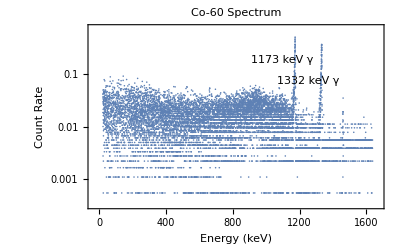

Ba-133

```mathematica
time=180;
datafile="Ba133.spe";
data=ToExpression[StringSplit[Import[datafolder<>datafile],"\n"][[13;;-15]]];
peaks=FindPeaks[data[[;;5000]]/time-bgdata[[;;5000]]/bgtime,50,10^-8,1]//N
energies={356,80.99,303,383.851,276.398};
TableForm[Multicolumn[Join[Sort[peaks[[;;,1]]],Sort[energies]],2]//First,TableHeadings->{None,{"Peak Channel","Energy (keV)"}}]
ratedata=data[[;;5000]]/time-bgdata[[;;5000]]/bgtime;
channels=Table[ft[x],{x,Length[ratedata]}];
ListLogPlot[Multicolumn[Join[channels,ratedata],2]//First,Frame->True,ImageSize->Full,FrameTicksStyle->Directive[16],FrameLabel->{Style["Energy (keV)",20],Style["Count Rate",20]},PlotLabel->Style["Ba-133 Spectrum",24],Joined->True,InterpolationOrder->0]
```

{{784.,10.8617},{2717.,1.74056},{2976.5,3.62},{3501.,9.24778},{3775.,1.26}}

Peak Channel | Energy (keV)
784. | 80.99
2717. | 276.398
2976.5 | 303
3501. | 356
3775. | 383.851

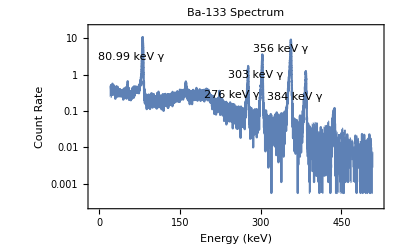

Cd-109

```mathematica
time=180;
datafile="Cd109.spe";
data=ToExpression[StringSplit[Import[datafolder<>datafile],"\n"][[13;;-15]]];
peaks=FindPeaks[data[[;;5000]]/time-bgdata[[;;5000]]/bgtime,50,10^-8,0.1]//N
energies={88.04};
TableForm[Multicolumn[Join[Sort[peaks[[;;,1]]],Sort[energies]],2]//First,TableHeadings->{None,{"Peak Channel","Energy (keV)"}}]
ratedata=data[[;;5000]]/time-bgdata[[;;5000]]/bgtime;
channels=Table[ft[x],{x,Length[ratedata]}];
ListLogPlot[Multicolumn[Join[channels,ratedata],2]//First,Frame->True,ImageSize->Full,FrameTicksStyle->Directive[16],FrameLabel->{Style["Energy (keV)",20],Style["Count Rate",20]},PlotLabel->Style["Cd-109 Spectrum",24]]
```

{{860.,0.637778}}

Peak Channel | Energy (keV)
860. | 88.04

Mn-54

```mathematica
time=180;
datafile="Mn54.spe";
data=ToExpression[StringSplit[Import[datafolder<>datafile],"\n"][[13;;-15]]];
peaks=FindPeaks[data[[;;10000]]/time-bgdata[[;;10000]]/bgtime, 50,10^-8,0.1]//N
energies={835};
TableForm[Multicolumn[Join[Sort[peaks[[;;,1]]],Sort[energies]],2]//First,TableHeadings->{None,{"Peak Channel","Energy (keV)"}}]
ratedata=data[[;;10000]]/time-bgdata[[;;10000]]/bgtime;
channels=Table[ft[x],{x,Length[ratedata]}];
ListLogPlot[Multicolumn[Join[channels,ratedata],2]//First,Frame->True,ImageSize->Full,FrameTicksStyle->Directive[16],FrameLabel->{Style["Energy (keV)",20],Style["Count Rate",20]},PlotLabel->Style["Mn-54 Spectrum",24],Joined->True,InterpolationOrder->0]
```

{{8214.,0.450556}}

Peak Channel | Energy (keV)
8214. | 835

```mathematica
peakdata={
{"Na-22",511,5026},
{"Na-22",1274,12546},
{"Cs-137",661.7,6510},
{"Co-57",122,1196},
{"Co-57",136,1338},
{"Co-60",1173,11550},
{"Co-60",1332,13119},
{"Ba-133",80.99,784},
{"Ba-133",276.4,2717},
{"Ba-133",303,2977},
{"Ba-133",356,3501},
{"Ba-133",384,3775},
{"Cd-109",88.04,860},
{"Mn-54",835,8214}
};
```

```mathematica
TableForm[peakdata,TableHeadings->{None,{"Isotope","Energy (keV)","Channel No."}}]
```

Isotope | Energy (keV) | Channel No.
Na-22 | 511 | 5026
Na-22 | 1274 | 12546
Cs-137 | 661.7 | 6510
Co-57 | 122 | 1196
Co-57 | 136 | 1338
Co-60 | 1173 | 11550
Co-60 | 1332 | 13119
Ba-133 | 80.99 | 784
Ba-133 | 276.4 | 2717
Ba-133 | 303 | 2977
Ba-133 | 356 | 3501
Ba-133 | 384 | 3775
Cd-109 | 88.04 | 860
Mn-54 | 835 | 8214

2. Using the data from 1, conduct a linear fit that will give you the best estimate for the conversion of voltage to channel number (that is, the slope in units of V/ch #). Report your answer below the calculations in a text-style cell.

Based on the following questions in the lab report, I have interpreted this as “Energy per channel” rather than V/ch #. As these two should be proportional, this should be transparent, but it will allow the analysis in part 1 to be used here.

```mathematica
ft=LinearModelFit[Multicolumn[Join[peakdata[[;;,3]],peakdata[[;;,2]]],2]//First,x,x]
```

FittedModel[0.814812+0.10149 x]

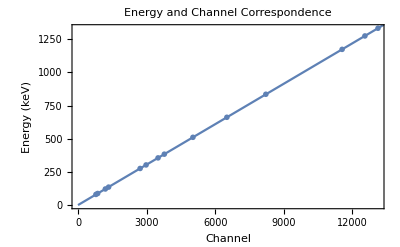

```mathematica
lp=ListPlot[Multicolumn[Join[peakdata[[;;,3]],peakdata[[;;,2]]],2]//First,PlotMarkers->Style[Orange],
Frame->True,FrameLabel->{Style["Channel",18],Style["Energy (keV)",18]},ImageSize->Full,PlotLabel->Style["Energy and Channel Correspondence",24],FrameTicksStyle->Directive[16],PlotLegends->Placed[{"Energy vs. Channel"},{0.15,0.85}]];
pp=Plot[ft[x],{x,0,2^14},PlotLegends->Placed[{"Linear Fit"},{0.15,0.85}]];
Show[lp,pp]
```